# DrawPauliTransferEval

```mathematica
SetDirectory @ NotebookDirectory[];
Import["../Link/QuESTlink.m"];
```

## Doc

```mathematica
?DrawPauliTransferEval
```

## Correctness

## Given evaluation data

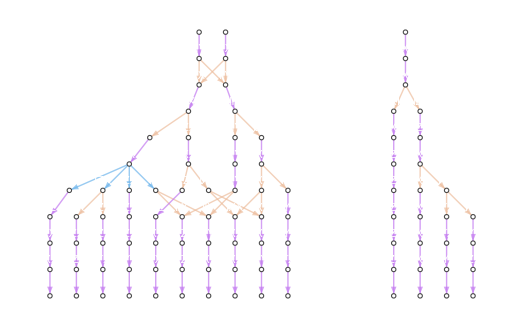

```mathematica
u = Circuit[Subscript[H, 0] Subscript[Rz, 0][a]Subscript[Ry, 1][b] Subscript[Damp, 1][c] Subscript[H, 1] Subscript[C, 1][Subscript[Ry, 0][a]]Subscript[Ph, 0][x] Subscript[H, 0] Subscript[C, 0][Subscript[X, 1]] Subscript[Z, 2]];
in = Subscript[Z, 0]+Subscript[Y, 0]+Subscript[X, 1];
data = CalcPauliTransferEval[in, u];
DrawPauliTransferEval[data]
```

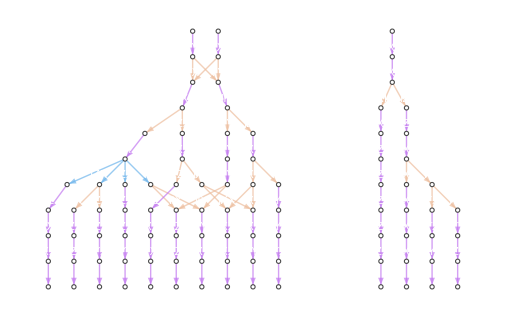

```mathematica
(* detailed data should yield an identical graph *)
data = CalcPauliTransferEval[in, u, "OutputForm"->"Detailed"];
DrawPauliTransferEval[data]
```

## Given circuit

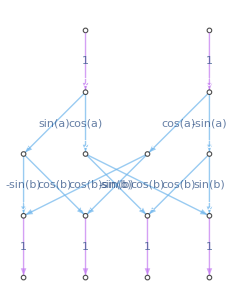

```mathematica
u = Circuit[Subscript[H, 0] Subscript[Ry, 0][a] Subscript[Rz, 1][b] Subscript[C, 0][Subscript[X, 1]]];
DrawPauliTransferEval[Subscript[X, 1] Subscript[Z, 0]+Subscript[Y, 1] Subscript[X, 0], u]
```

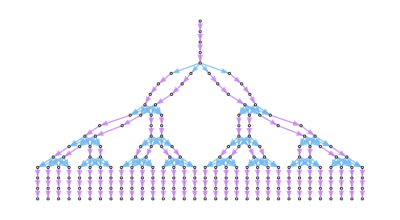

```mathematica
u = GetKnownCircuit["QFT", 5];
DrawPauliTransferEval[Subscript[X, 0],u]
```

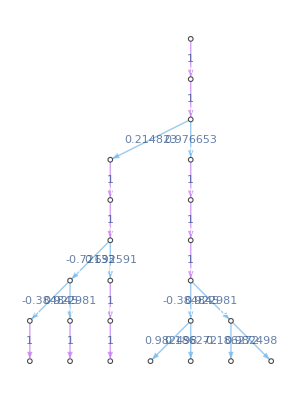

```mathematica
h = GetRandomPauliString[4,8];
u = GetKnownCircuit["Trotter", h, 1, 1, π];
DrawPauliTransferEval[Subscript[X, 0] Subscript[Y, 1] Subscript[Z, 2],u]
```

## Given PTMs and PTMaps

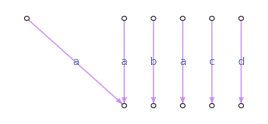

```mathematica
u = { Subscript[PTM, 0]@DiagonalMatrix@{a,b,c,d}};
DrawPauliTransferEval[Subscript[Id, 0]+Subscript[X, 0]+Subscript[Y, 0]+Subscript[Z, 0]+Subscript[Id, 1]+Subscript[X, 1], u]
```

```mathematica
u = Subscript[PTMap, 0][0->{{1,a}},1->{{2,b}},2->{{3,c}},3->{{0,d}}];
DrawPauliTransferEval[Subscript[Id, 0]+Subscript[X, 0]+Subscript[Y, 0]+Subscript[Z, 0], {u}]
```

-Graphics-

## Options

### “HighlightPathTo”

```mathematica
u = Circuit[Subscript[H, 0] Subscript[Rz, 0][a]Subscript[Ry, 1][b] Subscript[Damp, 1][c] Subscript[H, 1] Subscript[C, 1][Subscript[Ry, 0][a]]Subscript[Ph, 0][x] Subscript[H, 0] Subscript[C, 0][Subscript[X, 1]] Subscript[Z, 2]];
```

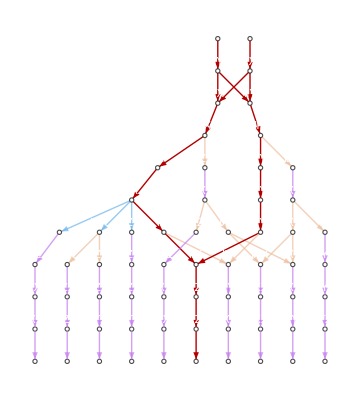

```mathematica
DrawPauliTransferEval[Subscript[Z, 0]+Subscript[Y, 0], u, "HighlightPathTo"->Subscript[Z, 0]]
```

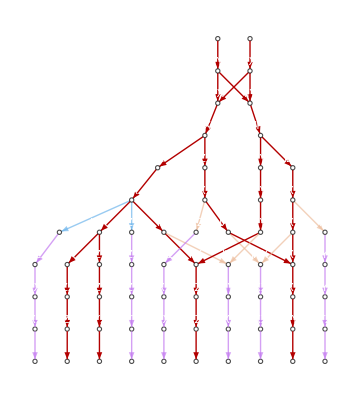

```mathematica
DrawPauliTransferEval[Subscript[Z, 0]+Subscript[Y, 0], u, 
	"HighlightPathTo"->{Subscript[Z, 0],Subscript[Y, 0], a Subscript[Z, 1]+b Subscript[X, 0] Subscript[Y, 1]}]
```

### “CombineStrings”

```mathematica
u = GetKnownCircuit["QFT", 4];
```

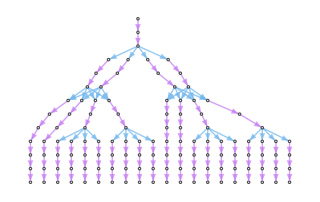

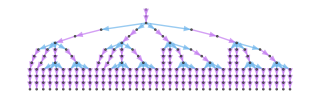

```mathematica
DrawPauliTransferEval[Subscript[Z, 0] Subscript[X, 1], u]
DrawPauliTransferEval[Subscript[Z, 0] Subscript[X, 1], u, "CombineStrings"->False]
```

### “PauliStringForm”

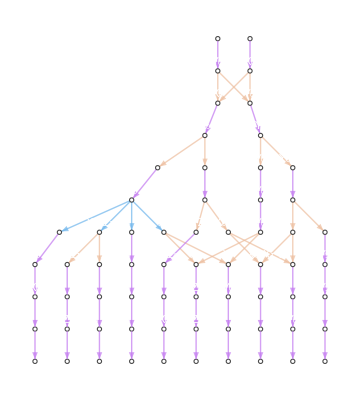

```mathematica
u = Circuit[Subscript[H, 0] Subscript[Rz, 0][a]Subscript[Ry, 1][b] Subscript[Damp, 1][c] Subscript[H, 1] Subscript[C, 1][Subscript[Ry, 0][a]]Subscript[Ph, 0][x] Subscript[H, 0] Subscript[C, 0][Subscript[X, 1]] Subscript[Z, 2]];

DrawPauliTransferEval[Subscript[Z, 0]+Subscript[Y, 0], u, "PauliStringForm"->"Subscript"]
```

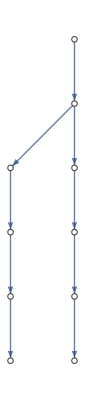
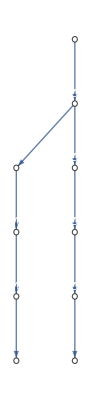
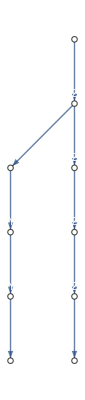
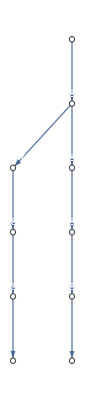
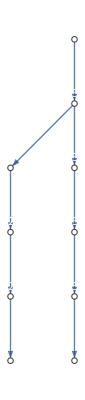
Hidden
-Graphics-  Subscript
-Graphics-  String
-Graphics-  Kronecker
-Graphics-  Index
-Graphics-

```mathematica
u = Circuit[Subscript[H, 0] Subscript[Rx, 0][a] Subscript[Damp, 0][b]Subscript[Depol, 0,1][c] Subscript[C, 0][Subscript[X, 1]]];
options = {"Hidden", "Subscript", "String", "Kronecker","Index"};

Row @ Riffle[Table[
	Column@{form,
		DrawPauliTransferEval[Subscript[X, 0], u, 
			"PauliStringForm"->form,
			"ShowCoefficients"->False]},
	{form, options}], "  "]
```

### “ShowCoefficients”

```mathematica
u = Circuit[Subscript[H, 0] Subscript[Rz, 0][a]Subscript[Ry, 1][b] Subscript[Damp, 1][c] Subscript[H, 1] Subscript[C, 1][Subscript[Ry, 0][a]]Subscript[Ph, 0][x] Subscript[H, 0] Subscript[C, 0][Subscript[X, 1]] Subscript[Z, 2]];
```

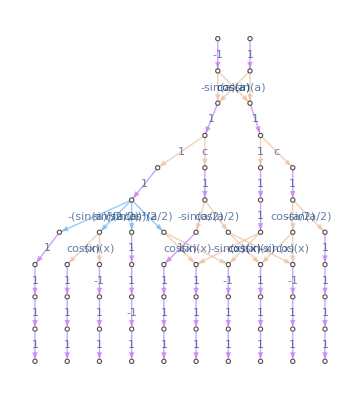

```mathematica
DrawPauliTransferEval[Subscript[Z, 0]+Subscript[Y, 0], u, 
	"ShowCoefficients"->True,
	"PauliStringForm"->"Hidden"]
```

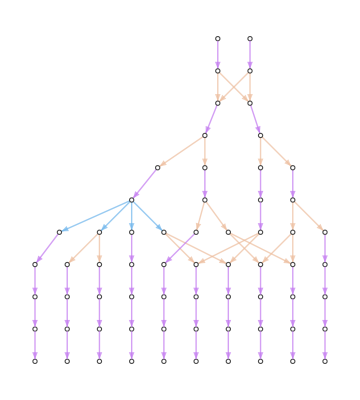

```mathematica
DrawPauliTransferEval[Subscript[Z, 0]+Subscript[Y, 0], u, 
	"ShowCoefficients"->False,
	"PauliStringForm"->"Hidden"]
```

### “EdgeDegreeStyles”

```mathematica
u = Circuit[Subscript[H, 0] Subscript[Rz, 0][a]Subscript[Ry, 1][b] Subscript[Damp, 1][c] Subscript[H, 1] Subscript[C, 1][Subscript[Ry, 0][a]]Subscript[Ph, 0][x] Subscript[H, 0] Subscript[C, 0][Subscript[X, 1]] Subscript[Z, 2]];
```

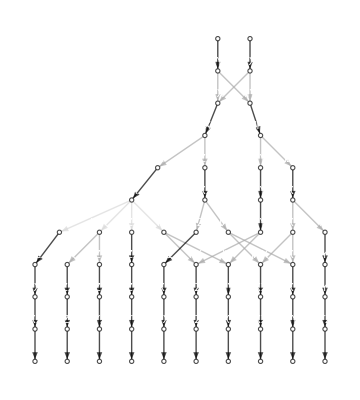

```mathematica
DrawPauliTransferEval[Subscript[Z, 0]+Subscript[Y, 0], u,
	"EdgeDegreeStyles"->{Black,Lighter@Gray,White, LightGray}]
```

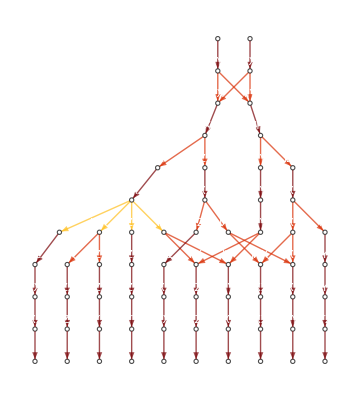

```mathematica
DrawPauliTransferEval[Subscript[Z, 0]+Subscript[Y, 0], u,
	"EdgeDegreeStyles"->ColorData["SolarColors"] /@ Range[0,1,.3]]
```

### “CacheMaps”

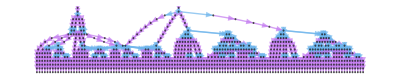
{1.56589,-Graphics-}

{2.26114,-Graphics-}

```mathematica
u = GetKnownCircuit["QFT", 5];
Timing @ DrawPauliTransferEval[Subscript[X, 3] Subscript[Z, 2]+Subscript[X, 2],u]
Timing @ DrawPauliTransferEval[Subscript[X, 3] Subscript[Z, 2]+Subscript[X, 2],u, "CacheMaps"->"Never"]
```

### AssertValidChannels

```mathematica
u = Circuit[Subscript[H, 0] Subscript[Rx, 0][a] Subscript[Damp, 0][b]Subscript[Depol, 0,1][c] Subscript[C, 0][Subscript[X, 1]]];

DrawPauliTransferEval[Subscript[X, 0], u]
```

-Graphics-

```mathematica
(* disabling simplification can cause zero weight branches to survive *)
```

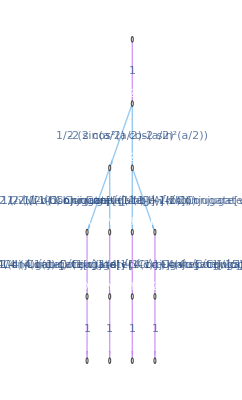

```mathematica
DrawPauliTransferEval[Subscript[X, 0], u, AssertValidChannels->False]
```

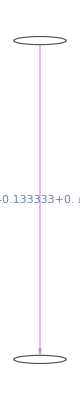

```mathematica
DrawPauliTransferEval[Subscript[X, 0], Subscript[Depol, 0][3/4 + .1], AssertValidChannels->False]
```

### Graph[] options

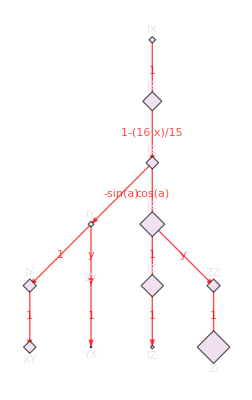

```mathematica
circ = Circuit[Subscript[H, 0] Subscript[Depol, 0,1][x]Subscript[Rx, 0][a] Subscript[Damp, 1][y]Subscript[C, 0][Subscript[X, 1]]];
DrawPauliTransferEval[Subscript[X, 0],circ,

	EdgeStyle->Red,
	VertexShapeFunction -> "Diamond",
	VertexSize :> .5 RandomReal[],
	VertexStyle ->LightPurple
]
```

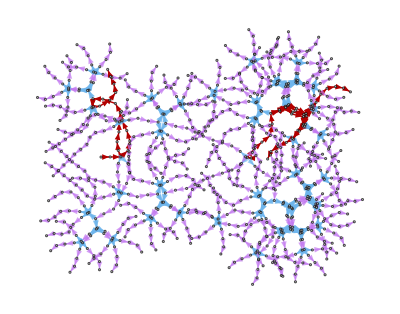

```mathematica
u = GetKnownCircuit["QFT", 5];

DrawPauliTransferEval[Subscript[X, 3] Subscript[Z, 2]+Subscript[X, 2],u, 
	"HighlightPathTo" -> {Subscript[X, 2],Subscript[Y, 1] Subscript[Y, 2], Subscript[X, 4] Subscript[X, 3] Subscript[X, 2] Subscript[Y, 1]},
	GraphLayout->"SpringEmbedding"
]
```

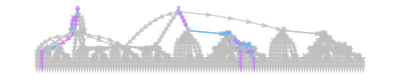

```mathematica
DrawPauliTransferEval[Subscript[X, 3] Subscript[Z, 2]+Subscript[X, 2],u, 
	"HighlightPathTo" -> {Subscript[X, 2],Subscript[Y, 1] Subscript[Y, 2], Subscript[X, 4] Subscript[X, 3] Subscript[X, 2] Subscript[Y, 1]},
	GraphHighlightStyle->"DehighlightGray"
]
```

## Warnings

DrawPauliTransferEval::error: Warning: the evaluation includes Pauli strings being mapped to null strings, as can occur from fully-mixing channels. The null strings and edges to them are not being rendered. Suppress this warning using Quiet[].

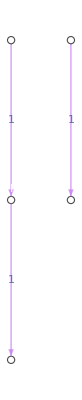

```mathematica
DrawPauliTransferEval[Subscript[X, 0]+Subscript[Id, 0],{Subscript[H, 0], Subscript[Depol, 0][3/4]}]
```

## Errors

```mathematica
DrawPauliTransferEval[Subscript[X, 0], Subscript[Depol, 0][3/4 + .1]]
```

CalcPauliTransferEval::error: Could not pre-compute the Pauli transfer maps due to the below error:

CalcPauliTransferMatrix::error: The channels could not be asserted as completely positive trace-preserving maps and hence were not simplified. Hide this warning with AssertValidChannels -> False, or use Quiet[].

DrawPauliTransferEval::error: Invalid arguments. See ?DrawPauliTransferEval

$Failed

```mathematica
DrawPauliTransferEval[Subscript[X, 0],Subscript[X, 0], "CombineStrings"->Eh]
```

DrawPauliTransferEval::error: Option "CombineStrings" must be True or False. See ?CalcPauliTransferEval.

$Failed

```mathematica
DrawPauliTransferEval[Subscript[X, 0],Subscript[X, 0], "CacheMaps"->Eh]
```

DrawPauliTransferEval::error: Option "CacheMaps" must be one of "Forever", "UntilCallEnd" or "Never". See ?ApplyPauliTransferMap.

$Failed

```mathematica
DrawPauliTransferEval[Subscript[X, 0],Subscript[X, 0], "ShowCoefficients"->Eh]
```

DrawPauliTransferEval::error: Option "ShowCoefficients" must be Automatic, True or False. See ?DrawPauliTransferEval.

$Failed

```mathematica
DrawPauliTransferEval[Subscript[X, 0],Subscript[X, 0], "PauliStringForm"->"Unknown"]
```

DrawPauliTransferEval::error: Invalid value for option "PauliStringForm". See ?DrawPauliTransferEval.

$Failed

```mathematica
DrawPauliTransferEval[Subscript[X, 0],Subscript[X, 0], "HighlightPathTo"->Eh]
DrawPauliTransferEval[Subscript[X, 0],Subscript[X, 0], "HighlightPathTo"->Subscript[X, -1]]
```

DrawPauliTransferEval::error: Invalid value for option "HighlightPathTo". See ?DrawPauliTransferEval.

$Failed

DrawPauliTransferEval::error: Invalid value for option "HighlightPathTo". See ?DrawPauliTransferEval.

$Failed

```mathematica
DrawPauliTransferEval[Subscript[X, 0],Subscript[X, 0], "UnrecognisedOption"->Eh]
```

OptionValue::nodef: Unknown option UnrecognisedOption for {DrawPauliTransferEval,CalcPauliTransferEval,ApplyPauliTransferMap,CalcPauliTransferMap,Graph}.

$Failed

```mathematica
DrawPauliTransferEval[Subscript[X, -1],{Subscript[X, 0]}]
```

DrawPauliTransferEval::error: Invalid arguments. See ?DrawPauliTransferEval

$Failed

```mathematica
DrawPauliTransferEval[Subscript[X, 0] Subscript[Y, 0],{Subscript[X, 0]}]
```

DrawPauliTransferEval::error: Invalid arguments. See ?DrawPauliTransferEval

$Failed

```mathematica
DrawPauliTransferEval[{Subscript[X, 0]},{}]
DrawPauliTransferEval[{},{Subscript[X, 0]}]
DrawPauliTransferEval[]
```

DrawPauliTransferEval::error: Invalid arguments. See ?DrawPauliTransferEval

$Failed

DrawPauliTransferEval::error: Invalid arguments. See ?DrawPauliTransferEval

$Failed

DrawPauliTransferEval::error: Invalid arguments. See ?DrawPauliTransferEval

$Failed